# Math 223: Homework 6

Hardeep Bassi

03/17/2023

## Problem 1

(a) Use integration by parts to find the leading behavior of  as  and compare your result with what Mathematica computes, which might be slightly different from what you compute. Comment on what you find and which approximation you believe yields a better approximation overall.

To find the first two terms of the leading behavior of , we can integrate by parts.
Let . This means we obtain:
. Integrating by parts again yields:
 This means we obtain:
. Hence we have that the leading behavior of  as . We can check this by plotting below using the Mathematica command FrenselS[x]:

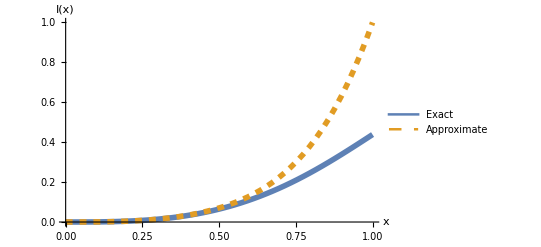

```mathematica
Plot[{FresnelS[x],(x*Sin[(π* x^2)/2]-(π* x^3)/3 Cos[(π *x^2)/2])},{x,0,1},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact", "Approximate"}]
```

(b) Using the splitting method from lecture, we see that the given integral is equivalent to:
. Using the hint, we take  This yields:
. Taking integration by parts on the second integral yields:
. This means we obtain:
, which means we have that  as . We can check this by plotting below using the Mathematica command FrenselS[x]:

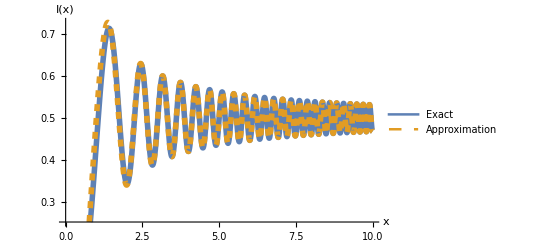

```mathematica
Plot[{FresnelS[x],1/2-Cos[π *1/2 x^2]/(π*x)},{x,0,10},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact", "Approximation"}]
```

These approximations make sense as part (a) was for , hence we expect the exact computed by Mathematica and approximate computed by integration by parts to align as we go to 0. For (b), we see our approximation was for , so we see that the Mathematica exact and the approximate computed by integration by parts aligns better as we take .

## Problem 2

Restate the problem here and follow up with any computations or explanations.